```mathematica
(*High Resolution 13C Data- Michael's 75:25 samples*)
```

```mathematica
(*Obviously you will need to download and evaluate CustomTicks for this part to work*)
Needs["CustomTicks`"]
```

```mathematica
(*Setting options for plots ahead- most plots use this but some don't so check*)
SetOptions[LinTicks,TickReverse->True,MajorTickLength->{0.035,0.},MinorTickLength->{0.013,0.}];
SetOptions[LogTicks,TickReverse->True,MajorTickLength->{0.035,0.},MinorTickLength->{0.013,0.}];
SetOptions[ListPlot, Frame->{{False,False},{True,False}},FrameTicks->{{None,None},{LinTicks,None}}, FrameStyle->Black, AspectRatio->0.5, LabelStyle->Directive[FontSize->17, FontFamily->"Arial"]];
SetOptions[Plot, Frame->{{False,False},{True,False}}, FrameTicks->{{None,None},{LinTicks,None}},FrameStyle->Black, AspectRatio->0.4, LabelStyle->Directive[FontSize->17, FontFamily->"Arial"]];
```

```mathematica
(*You will need to change this part to refer to the location of data files on your own computer*)
```

```mathematica
SetDirectory["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\Michael 13C samples\\Michael High res samples"];
FileNames[]
```

{LK-MB-6040_1h_PLGAhr,LK-MB-6040-1hr.csv,LK-MB-6040-24h.csv,LK-MB_6040_24h_PLGAhr,LK-MB-6040-2h.csv,LK-MB_6040_2h_PLGAhr,LK-MB-6040-30min.csv,LK-MB_6040_30m_PLGAhr,Lk-MB_6040_48h_PLGAhr,LK-MB-6040-48hr.csv,LK-MB-6040-6h.csv,LK-MB_6040_6h_PLGAhr,LK-MB-7525-120h.csv,LK-MB-7525_120hr_hr,LK-MB-7525_1h,LK-MB-7525-1hr.csv,LK-MB-7525_24h,LK-MB-7525-24h.csv,LK-MB-7525_30min,LK-MB-7525-30min.csv,LK-MB-7525_48h,LK-MB-7525-48h.csv,LK-MB-7525_6h,LK-MB-7525-6h.csv,LK-MB-7525-72h.csv,LK-MB-7525_72hr_hr,MB_6040_highres.mnova,MB-7525-30mincomp.csv,MBhighres.mnova,output.csv}

```mathematica
(*Even though the files are .csv importing as tsv seems to work better*)
MBp5=Import["LK-MB-7525-30min.csv","TSV"];
MB1h=Import["LK-MB-7525-1hr.csv","TSV"];
MB6h=Import["LK-MB-7525-6h.csv","TSV"];
MB24h=Import["LK-MB-7525-24h.csv","TSV"];
MB48h=Import["LK-MB-7525-48h.csv","TSV"];

(*You can use this to set limits for signal that is being deconvoluted- different from 60:40 because sweep width was different*)
start=20435; end=20930;
MBp5[[start,1;;2]]
MBp5[[end,1;;2]]
```

{60.7061,19.1064}

{61.0827,5.57617}

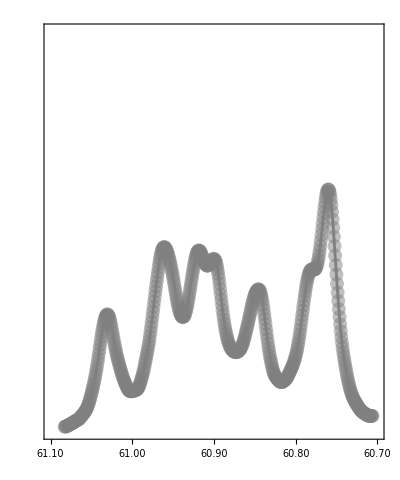

```mathematica
(*Just plot a sample to make sure we have the right limits*)
a0p5=ListPlot[MBp5[[start;;end,1;;2]],PlotRange->{{60.7,61.1},{0,500.}},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},Axes->{True,False},ScalingFunctions->{"Reverse",None}];
b0p5=ListPlot[MBp5[[start;;end,1;;2]],PlotRange->{{60.7,61.1},{0,500.}},AspectRatio->1.2,PlotStyle->{Gray},Joined->True,ScalingFunctions->{"Reverse",None}];
dataplotMBp5=Show[{a0p5,b0p5}]
```

```mathematica
(*Set starting points for peak locations (These will change slightly over time just a starting point)*)
ppm1=60.7575;
ppm2=60.7745;
ppm3=60.807;
ppm4=60.8437;
ppm5=60.8682;
ppm6=60.8886;
ppm7=60.9277;
ppm8=60.9571;
ppm9 = 61.0158;
```

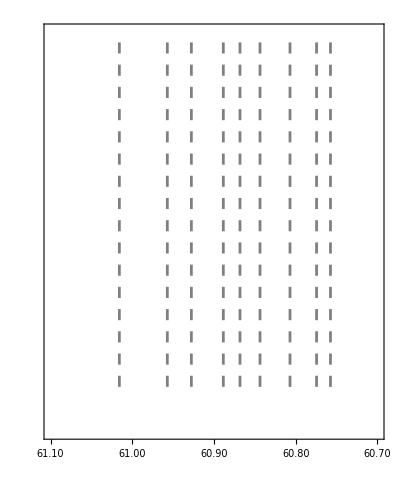

```mathematica
(*Dashed lines at starting peak locations*)
dashed=ListPlot[{{{ppm1,0},{ppm1,5000}},{{ppm2,0},{ppm2,5000}},{{ppm3,0},{ppm3,5000}},{{ppm4,0},{ppm4,5000}},{{ppm5,0},{ppm5,5000}},{{ppm6,0},{ppm6,5000}},{{ppm7,0},{ppm7,5000}},{{ppm8,0},{ppm8,5000}},{{ppm9,0},{ppm9,5000}}},Joined->True,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]}},PlotRange->{{60.7,61.1},{-500,4000.}},AspectRatio->1.2]
```

```mathematica
(*Definition of Lorentzian*)
Lorentzian[scale_,ppm_,ppmavg_,width_]:=scale (width/(2 Pi ((ppm-ppmavg)^2+(width/2)^2)))
```

```mathematica
(*Now we start the fits*)
```

{scale1→9.97078,scale2→5.51544,scale3→6.98508,scale5→6.2906,scale6→6.0574,scale7→10.573,scale8→4.99232,ppmavg1→60.7597,ppmavg2→60.7837,ppmavg3→60.8475,ppmavg5→60.8987,ppmavg6→60.9203,ppmavg7→60.9609,ppmavg8→61.0307,width1→0.0234216,width2→0.0259468,width3→0.0292458,width5→0.0278505,width6→0.0265627,width7→0.0322348,width8→0.0234058}

0.998921

General::munfl: Exp[-4884.91] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4506.31] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4734.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 9.97078 | 0.151768 | 65.6974 | 1.57123×10^-240
scale2 | 5.51544 | 0.168434 | 32.7454 | 6.85672×10^-124
scale3 | 6.98508 | 0.0996493 | 70.0966 | 1.18508×10^-252
scale5 | 6.2906 | 0.315401 | 19.9447 | 9.57733×10^-65
scale6 | 6.0574 | 0.339361 | 17.8494 | 6.59584×10^-55
scale7 | 10.573 | 0.130923 | 80.7574 | 1.34975×10^-279
scale8 | 4.99232 | 0.0592318 | 84.2845 | 7.69001×10^-288
ppmavg1 | 60.7597 | 0.00009594 | 633309. | 0.
ppmavg2 | 60.7837 | 0.000212974 | 285404. | 0.
ppmavg3 | 60.8475 | 0.000131869 | 461423. | 0.
ppmavg5 | 60.8987 | 0.000310109 | 196378. | 0.
ppmavg6 | 60.9203 | 0.000279301 | 218117. | 0.
ppmavg7 | 60.9609 | 0.000117868 | 517196. | 0.
ppmavg8 | 61.0307 | 0.000121297 | 503152. | 0.
width1 | 0.0234216 | 0.000285741 | 81.9679 | 1.8459×10^-282
width2 | 0.0259468 | 0.000668156 | 38.8335 | 1.66418×10^-149
width3 | 0.0292458 | 0.000477174 | 61.2895 | 1.03222×10^-227
width5 | 0.0278505 | 0.000891352 | 31.2453 | 2.81076×10^-117
width6 | 0.0265627 | 0.00100113 | 26.5327 | 8.06204×10^-96
width7 | 0.0322348 | 0.000404709 | 79.6492 | 6.0986×10^-277
width8 | 0.0234058 | 0.000371292 | 63.0386 | 6.96983×10^-233

| DF | SS | MS
Model | 21 | 1.03014×10^7 | 490542.
Error | 475 | 11123.5 | 23.4179
Uncorrected Total | 496 | 1.03125×10^7 | 
Corrected Total | 495 | 2.65301×10^6 |

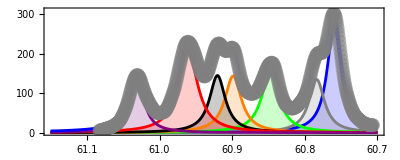

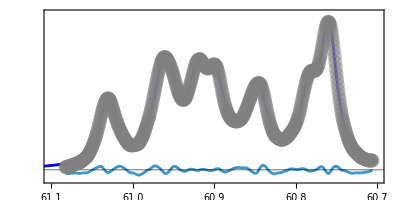

```mathematica
fit1=NonlinearModelFit[MBp5[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]},{{scale1,30.},{scale2,30.},{scale3,30.},{scale5,50.},{scale6,10},{scale7,25.},{scale8,16.},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{width1,0.02},{width2,0.01},{width3,0.01},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01}},x];
fit1["BestFitParameters"]
fit1["RSquared"]
fit1["ParameterTable"]
fit1["ANOVATable"]
individualMBp5=Plot[{Lorentzian[fit1["BestFitParameters"][[1]][[2]],ppm,fit1["BestFitParameters"][[8]][[2]],fit1["BestFitParameters"][[15]][[2]]],Lorentzian[fit1["BestFitParameters"][[2]][[2]],ppm,fit1["BestFitParameters"][[9]][[2]],fit1["BestFitParameters"][[16]][[2]]],Lorentzian[fit1["BestFitParameters"][[3]][[2]],ppm,fit1["BestFitParameters"][[10]][[2]],fit1["BestFitParameters"][[17]][[2]]],Lorentzian[fit1["BestFitParameters"][[4]][[2]],ppm,fit1["BestFitParameters"][[11]][[2]],fit1["BestFitParameters"][[18]][[2]]],Lorentzian[fit1["BestFitParameters"][[5]][[2]],ppm,fit1["BestFitParameters"][[12]][[2]],fit1["BestFitParameters"][[19]][[2]]],Lorentzian[fit1["BestFitParameters"][[6]][[2]],ppm,fit1["BestFitParameters"][[13]][[2]],fit1["BestFitParameters"][[20]][[2]]],Lorentzian[fit1["BestFitParameters"][[7]][[2]],ppm,fit1["BestFitParameters"][[14]][[2]],fit1["BestFitParameters"][[21]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,320.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},Frame->{{False,False},{True,False}},FrameLabel->{"ppm",None},AspectRatio->0.4,PlotStyle->{Blue,Gray,Green,Orange,Black,Red,Purple,Brown}];
cumulativeMBp5=Plot[Lorentzian[fit1["BestFitParameters"][[1]][[2]],ppm,fit1["BestFitParameters"][[8]][[2]],fit1["BestFitParameters"][[15]][[2]]]+Lorentzian[fit1["BestFitParameters"][[2]][[2]],ppm,fit1["BestFitParameters"][[9]][[2]],fit1["BestFitParameters"][[16]][[2]]]+Lorentzian[fit1["BestFitParameters"][[3]][[2]],ppm,fit1["BestFitParameters"][[10]][[2]],fit1["BestFitParameters"][[17]][[2]]]+Lorentzian[fit1["BestFitParameters"][[4]][[2]],ppm,fit1["BestFitParameters"][[11]][[2]],fit1["BestFitParameters"][[18]][[2]]]+Lorentzian[fit1["BestFitParameters"][[5]][[2]],ppm,fit1["BestFitParameters"][[12]][[2]],fit1["BestFitParameters"][[19]][[2]]]+Lorentzian[fit1["BestFitParameters"][[6]][[2]],ppm,fit1["BestFitParameters"][[13]][[2]],fit1["BestFitParameters"][[20]][[2]]]+Lorentzian[fit1["BestFitParameters"][[7]][[2]],ppm,fit1["BestFitParameters"][[14]][[2]],fit1["BestFitParameters"][[21]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,320.}},PlotStyle->{Blue},AspectRatio->1.2,ScalingFunctions->{"Reverse",None},Axes->{True,False}];
residualsMBp5=ListPlot[Thread[{MBp5[[start;;end,1]],fit1["FitResiduals"]}],Joined->True, PlotRange->{{60.7,61.101},{-20,320}},ScalingFunctions->{"Reverse",None}];
baseplot = ListPlot[{{60.5,0},{61.2,0}},Joined->True,ScalingFunctions->{"Reverse",None},PlotStyle->Directive[Black,Thickness[0.001]]];
Show[{individualMBp5,cumulativeMBp5,a0p5}]
Show[{residualsMBp5,cumulativeMBp5,a0p5,baseplot}]
```

FittedModel[…]

{scale1→10.0528,scale2→5.84637,scale3→7.51362,scale5→8.4191,scale6→4.66264,scale7→11.025,scale8→5.685,ppmavg1→60.7605,ppmavg2→60.7842,ppmavg3→60.8486,ppmavg5→60.8997,ppmavg6→60.9217,ppmavg7→60.9616,ppmavg8→61.0305,width1→0.0234545,width2→0.0261038,width3→0.0299802,width5→0.0343254,width6→0.025335,width7→0.0325857,width8→0.0263179}

0.998705

General::munfl: Exp[-4816.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4456.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4663.64] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 10.0528 | 0.178311 | 56.3782 | 1.46155×10^-212
scale2 | 5.84637 | 0.198183 | 29.4998 | 1.9154×10^-109
scale3 | 7.51362 | 0.141043 | 53.2718 | 1.83003×10^-202
scale5 | 8.4191 | 0.493672 | 17.054 | 3.19204×10^-51
scale6 | 4.66264 | 0.436998 | 10.6697 | 5.70704×10^-24
scale7 | 11.025 | 0.147111 | 74.9434 | 2.65112×10^-265
scale8 | 5.685 | 0.074734 | 76.0698 | 3.81978×10^-268
ppmavg1 | 60.7605 | 0.000110721 | 548772. | 0.
ppmavg2 | 60.7842 | 0.000236597 | 256910. | 0.
ppmavg3 | 60.8486 | 0.00015309 | 397470. | 0.
ppmavg5 | 60.8997 | 0.000469549 | 129698. | 0.
ppmavg6 | 60.9217 | 0.000384139 | 158593. | 0.
ppmavg7 | 60.9616 | 0.000130257 | 468010. | 0.
ppmavg8 | 61.0305 | 0.000145859 | 418422. | 0.
width1 | 0.0234545 | 0.000327996 | 71.5085 | 2.06718×10^-256
width2 | 0.0261038 | 0.000736081 | 35.4633 | 1.42502×10^-135
width3 | 0.0299802 | 0.000576495 | 52.0043 | 3.19628×10^-198
width5 | 0.0343254 | 0.00126463 | 27.1428 | 1.19323×10^-98
width6 | 0.025335 | 0.00143049 | 17.7107 | 2.91256×10^-54
width7 | 0.0325857 | 0.000452896 | 71.9497 | 1.42404×10^-257
width8 | 0.0263179 | 0.000454521 | 57.9024 | 2.28649×10^-217

| DF | SS | MS
Model | 21 | 1.11734×10^7 | 532065.
Error | 475 | 14493.7 | 30.5131
Uncorrected Total | 496 | 1.11879×10^7 | 
Corrected Total | 495 | 2.70729×10^6 |

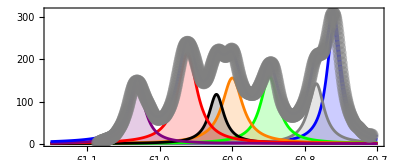

```mathematica
fit2=NonlinearModelFit[MB1h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]},{{scale1,30.},{scale2,30.},{scale3,30.},{scale5,50.},{scale6,10},{scale7,25.},{scale8,16.},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{width1,0.02},{width2,0.01},{width3,0.01},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01}},x]
fit2["BestFitParameters"]
fit2["RSquared"]
fit2["ParameterTable"]
fit2["ANOVATable"]
individualMB1h=Plot[{Lorentzian[fit2["BestFitParameters"][[1]][[2]],ppm,fit2["BestFitParameters"][[8]][[2]],fit2["BestFitParameters"][[15]][[2]]],Lorentzian[fit2["BestFitParameters"][[2]][[2]],ppm,fit2["BestFitParameters"][[9]][[2]],fit2["BestFitParameters"][[16]][[2]]],Lorentzian[fit2["BestFitParameters"][[3]][[2]],ppm,fit2["BestFitParameters"][[10]][[2]],fit2["BestFitParameters"][[17]][[2]]],Lorentzian[fit2["BestFitParameters"][[4]][[2]],ppm,fit2["BestFitParameters"][[11]][[2]],fit2["BestFitParameters"][[18]][[2]]],Lorentzian[fit2["BestFitParameters"][[5]][[2]],ppm,fit2["BestFitParameters"][[12]][[2]],fit2["BestFitParameters"][[19]][[2]]],Lorentzian[fit2["BestFitParameters"][[6]][[2]],ppm,fit2["BestFitParameters"][[13]][[2]],fit2["BestFitParameters"][[20]][[2]]],Lorentzian[fit2["BestFitParameters"][[7]][[2]],ppm,fit2["BestFitParameters"][[14]][[2]],fit2["BestFitParameters"][[21]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,350.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Orange,Black,Red,Purple,Brown}];
cumulativeMB1h=Plot[Lorentzian[fit2["BestFitParameters"][[1]][[2]],ppm,fit2["BestFitParameters"][[8]][[2]],fit2["BestFitParameters"][[15]][[2]]]+Lorentzian[fit2["BestFitParameters"][[2]][[2]],ppm,fit2["BestFitParameters"][[9]][[2]],fit2["BestFitParameters"][[16]][[2]]]+Lorentzian[fit2["BestFitParameters"][[3]][[2]],ppm,fit2["BestFitParameters"][[10]][[2]],fit2["BestFitParameters"][[17]][[2]]]+Lorentzian[fit2["BestFitParameters"][[4]][[2]],ppm,fit2["BestFitParameters"][[11]][[2]],fit2["BestFitParameters"][[18]][[2]]]+Lorentzian[fit2["BestFitParameters"][[5]][[2]],ppm,fit2["BestFitParameters"][[12]][[2]],fit2["BestFitParameters"][[19]][[2]]]+Lorentzian[fit2["BestFitParameters"][[6]][[2]],ppm,fit2["BestFitParameters"][[13]][[2]],fit2["BestFitParameters"][[20]][[2]]]+Lorentzian[fit2["BestFitParameters"][[7]][[2]],ppm,fit2["BestFitParameters"][[14]][[2]],fit2["BestFitParameters"][[21]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,350.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB1h,cumulativeMB1h,ListPlot[MB1h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{-500,4500.}},Axes->{True,False},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

FittedModel[…]

{scale1→16.1184,scale2→11.907,scale3→12.9854,scale4→7.65232,scale5→11.9486,scale6→8.93994,scale7→21.1764,scale8→11.7745,scale2a→0.133366,ppmavg1→60.7616,ppmavg2→60.7836,ppmavg3→60.8478,ppmavg4→60.8733,ppmavg5→60.9,ppmavg6→60.921,ppmavg7→60.9621,ppmavg8→61.0286,ppmavg2a→60.8118,width1→0.0228021,width2→0.0301567,width3→0.0291132,width4→0.0383607,width5→0.0299138,width6→0.028622,width7→0.0367494,width8→0.0310753,width2a→0.00906582}

0.999104

General::munfl: Exp[-4686.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4251.52] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4204.59] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 16.1184 | 0.465876 | 34.5981 | 3.49136×10^-131
scale2 | 11.907 | 0.619753 | 19.2126 | 4.14409×10^-61
scale3 | 12.9854 | 1.21841 | 10.6576 | 6.77304×10^-24
scale4 | 7.65232 | 2.85913 | 2.67645 | 0.00770118
scale5 | 11.9486 | 2.39183 | 4.99558 | 8.29228×10^-7
scale6 | 8.93994 | 1.20474 | 7.42066 | 5.51862×10^-13
scale7 | 21.1764 | 0.339361 | 62.4007 | 2.84861×10^-229
scale8 | 11.7745 | 0.146885 | 80.161 | 6.88922×10^-276
scale2a | 0.133366 | 0.118415 | 1.12626 | 0.260632
ppmavg1 | 60.7616 | 0.000129156 | 470451. | 0.
ppmavg2 | 60.7836 | 0.000326845 | 185971. | 0.
ppmavg3 | 60.8478 | 0.000361629 | 168260. | 0.
ppmavg4 | 60.8733 | 0.00117498 | 51808.1 | 0.
ppmavg5 | 60.9 | 0.000464986 | 130972. | 0.
ppmavg6 | 60.921 | 0.000633042 | 96235.4 | 0.
ppmavg7 | 60.9621 | 0.000148151 | 411485. | 0.
ppmavg8 | 61.0286 | 0.000146589 | 416324. | 0.
ppmavg2a | 60.8118 | 0.00207535 | 29301.9 | 0.
width1 | 0.0228021 | 0.000397996 | 57.2923 | 6.86025×10^-214
width2 | 0.0301567 | 0.00119431 | 25.2502 | 1.82761×10^-89
width3 | 0.0291132 | 0.001244 | 23.4029 | 8.00887×10^-81
width4 | 0.0383607 | 0.00861443 | 4.45307 | 0.0000105924
width5 | 0.0299138 | 0.00319029 | 9.37653 | 2.91032×10^-19
width6 | 0.028622 | 0.00192156 | 14.8952 | 2.30567×10^-41
width7 | 0.0367494 | 0.0005328 | 68.974 | 1.14177×10^-247
width8 | 0.0310753 | 0.000477786 | 65.0402 | 7.73734×10^-237
width2a | 0.00906582 | 0.00805822 | 1.12504 | 0.261147

| DF | SS | MS
Model | 27 | 3.99237×10^7 | 1.47866×10^6
Error | 469 | 35817.5 | 76.37
Uncorrected Total | 496 | 3.99595×10^7 | 
Corrected Total | 495 | 8.56362×10^6 |

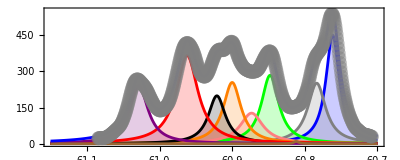

```mathematica
fit3=NonlinearModelFit[MB6h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale4,x,ppmavg4,width4]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]+Lorentzian[scale2a,x,ppmavg2a,width2a]},{{scale1,30.},{scale2,30.},{scale3,30.},{scale4,10.},{scale5,50.},{scale6,10},{scale7,25.},{scale8,16.},{scale2a,5.},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg4,60.87},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{ppmavg2a,60.81},{width1,0.02},{width2,0.01},{width3,0.01},{width4,0.01},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01},{width2a,0.01}},x,Method->"LevenbergMarquardt"]
fit3["BestFitParameters"]
fit3["RSquared"]
fit3["ParameterTable"]
fit3["ANOVATable"]
individualMB6h=Plot[{Lorentzian[fit3["BestFitParameters"][[1]][[2]],ppm,fit3["BestFitParameters"][[10]][[2]],fit3["BestFitParameters"][[19]][[2]]],Lorentzian[fit3["BestFitParameters"][[2]][[2]],ppm,fit3["BestFitParameters"][[11]][[2]],fit3["BestFitParameters"][[20]][[2]]],Lorentzian[fit3["BestFitParameters"][[3]][[2]],ppm,fit3["BestFitParameters"][[12]][[2]],fit3["BestFitParameters"][[21]][[2]]],Lorentzian[fit3["BestFitParameters"][[4]][[2]],ppm,fit3["BestFitParameters"][[13]][[2]],fit3["BestFitParameters"][[22]][[2]]],Lorentzian[fit3["BestFitParameters"][[5]][[2]],ppm,fit3["BestFitParameters"][[14]][[2]],fit3["BestFitParameters"][[23]][[2]]],Lorentzian[fit3["BestFitParameters"][[6]][[2]],ppm,fit3["BestFitParameters"][[15]][[2]],fit3["BestFitParameters"][[24]][[2]]],Lorentzian[fit3["BestFitParameters"][[7]][[2]],ppm,fit3["BestFitParameters"][[16]][[2]],fit3["BestFitParameters"][[25]][[2]]],Lorentzian[fit3["BestFitParameters"][[8]][[2]],ppm,fit3["BestFitParameters"][[17]][[2]],fit3["BestFitParameters"][[26]][[2]]],Lorentzian[fit3["BestFitParameters"][[9]][[2]],ppm,fit3["BestFitParameters"][[18]][[2]],fit3["BestFitParameters"][[27]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,570.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Pink,Orange,Black,Red,Purple,Brown}];
cumulativeMB6h=Plot[Lorentzian[fit3["BestFitParameters"][[1]][[2]],ppm,fit3["BestFitParameters"][[10]][[2]],fit3["BestFitParameters"][[19]][[2]]]+Lorentzian[fit3["BestFitParameters"][[2]][[2]],ppm,fit3["BestFitParameters"][[11]][[2]],fit3["BestFitParameters"][[20]][[2]]]+Lorentzian[fit3["BestFitParameters"][[3]][[2]],ppm,fit3["BestFitParameters"][[12]][[2]],fit3["BestFitParameters"][[21]][[2]]]+Lorentzian[fit3["BestFitParameters"][[4]][[2]],ppm,fit3["BestFitParameters"][[13]][[2]],fit3["BestFitParameters"][[22]][[2]]]+Lorentzian[fit3["BestFitParameters"][[5]][[2]],ppm,fit3["BestFitParameters"][[14]][[2]],fit3["BestFitParameters"][[23]][[2]]]+Lorentzian[fit3["BestFitParameters"][[6]][[2]],ppm,fit3["BestFitParameters"][[15]][[2]],fit3["BestFitParameters"][[24]][[2]]]+Lorentzian[fit3["BestFitParameters"][[7]][[2]],ppm,fit3["BestFitParameters"][[16]][[2]],fit3["BestFitParameters"][[25]][[2]]]+Lorentzian[fit3["BestFitParameters"][[8]][[2]],ppm,fit3["BestFitParameters"][[17]][[2]],fit3["BestFitParameters"][[26]][[2]]]+Lorentzian[fit3["BestFitParameters"][[9]][[2]],ppm,fit3["BestFitParameters"][[18]][[2]],fit3["BestFitParameters"][[27]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,570.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB6h,cumulativeMB6h,ListPlot[MB6h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{0,500.}},Axes->{True,False},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

FittedModel[…]

{scale1→5.94935,scale2→5.63026,scale3→5.69995,scale4→6.42044,scale5→6.60612,scale6→4.27142,scale7→11.3259,scale8→5.39984,scale2a→1.30129,ppmavg1→60.7613,ppmavg2→60.7804,ppmavg3→60.8467,ppmavg4→60.8724,ppmavg5→60.8961,ppmavg6→60.9198,ppmavg7→60.9607,ppmavg8→61.0239,ppmavg2a→60.807,width1→0.021637,width2→0.029139,width3→0.0297299,width4→0.0379186,width5→0.0370429,width6→0.0392368,width7→0.0437428,width8→0.0328613,width2a→0.032771}

0.999188

General::munfl: Exp[-4449.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4142.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4084.06] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 5.94935 | 0.386766 | 15.3823 | 1.59374×10^-43
scale2 | 5.63026 | 0.758619 | 7.42172 | 5.479×10^-13
scale3 | 5.69995 | 0.773353 | 7.37043 | 7.74179×10^-13
scale4 | 6.42044 | 2.50453 | 2.56353 | 0.0106721
scale5 | 6.60612 | 3.09951 | 2.13134 | 0.0335801
scale6 | 4.27142 | 1.65366 | 2.583 | 0.0100962
scale7 | 11.3259 | 0.3606 | 31.4085 | 2.06108×10^-117
scale8 | 5.39984 | 0.0900218 | 59.9837 | 4.04214×10^-222
scale2a | 1.30129 | 0.502911 | 2.58751 | 0.00996683
ppmavg1 | 60.7613 | 0.000214065 | 283846. | 0.
ppmavg2 | 60.7804 | 0.000412426 | 147373. | 0.
ppmavg3 | 60.8467 | 0.000467588 | 130129. | 0.
ppmavg4 | 60.8724 | 0.00126737 | 48030.7 | 0.
ppmavg5 | 60.8961 | 0.00105124 | 57927.9 | 0.
ppmavg6 | 60.9198 | 0.00207016 | 29427.6 | 0.
ppmavg7 | 60.9607 | 0.000278093 | 219210. | 0.
ppmavg8 | 61.0239 | 0.000177084 | 344604. | 0.
ppmavg2a | 60.807 | 0.00191074 | 31823.7 | 0.
width1 | 0.021637 | 0.000676322 | 31.9922 | 5.68262×10^-120
width2 | 0.029139 | 0.00243614 | 11.9611 | 5.80972×10^-29
width3 | 0.0297299 | 0.00190824 | 15.5798 | 2.09036×10^-44
width4 | 0.0379186 | 0.00707455 | 5.35986 | 1.30889×10^-7
width5 | 0.0370429 | 0.00797585 | 4.64438 | 4.43602×10^-6
width6 | 0.0392368 | 0.00618046 | 6.34852 | 5.13764×10^-10
width7 | 0.0437428 | 0.000917543 | 47.6738 | 5.99093×10^-182
width8 | 0.0328613 | 0.000603273 | 54.4717 | 6.00673×10^-205
width2a | 0.032771 | 0.00792504 | 4.13512 | 0.0000420384

| DF | SS | MS
Model | 27 | 1.03359×10^7 | 382812.
Error | 469 | 8401.73 | 17.9141
Uncorrected Total | 496 | 1.03443×10^7 | 
Corrected Total | 495 | 2.17742×10^6 |

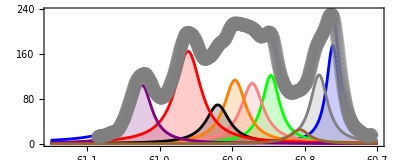

```mathematica
fit4=NonlinearModelFit[MB24h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale4,x,ppmavg4,width4]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]+Lorentzian[scale2a,x,ppmavg2a,width2a]},{{scale1,30.},{scale2,30.},{scale3,30.},{scale4,10.},{scale5,50.},{scale6,10},{scale7,25.},{scale8,16.},{scale2a,10},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg4,60.87},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{ppmavg2a,60.81},{width1,0.02},{width2,0.01},{width3,0.01},{width4,0.01},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01},{width2a,0.01}},x]
fit4["BestFitParameters"]
fit4["RSquared"]
fit4["ParameterTable"]
fit4["ANOVATable"]
individualMB24h=Plot[{Lorentzian[fit4["BestFitParameters"][[1]][[2]],ppm,fit4["BestFitParameters"][[10]][[2]],fit4["BestFitParameters"][[19]][[2]]],Lorentzian[fit4["BestFitParameters"][[2]][[2]],ppm,fit4["BestFitParameters"][[11]][[2]],fit4["BestFitParameters"][[20]][[2]]],Lorentzian[fit4["BestFitParameters"][[3]][[2]],ppm,fit4["BestFitParameters"][[12]][[2]],fit4["BestFitParameters"][[21]][[2]]],Lorentzian[fit4["BestFitParameters"][[4]][[2]],ppm,fit4["BestFitParameters"][[13]][[2]],fit4["BestFitParameters"][[22]][[2]]],Lorentzian[fit4["BestFitParameters"][[5]][[2]],ppm,fit4["BestFitParameters"][[14]][[2]],fit4["BestFitParameters"][[23]][[2]]],Lorentzian[fit4["BestFitParameters"][[6]][[2]],ppm,fit4["BestFitParameters"][[15]][[2]],fit4["BestFitParameters"][[24]][[2]]],Lorentzian[fit4["BestFitParameters"][[7]][[2]],ppm,fit4["BestFitParameters"][[16]][[2]],fit4["BestFitParameters"][[25]][[2]]],Lorentzian[fit4["BestFitParameters"][[8]][[2]],ppm,fit4["BestFitParameters"][[17]][[2]],fit4["BestFitParameters"][[26]][[2]]],Lorentzian[fit4["BestFitParameters"][[9]][[2]],ppm,fit4["BestFitParameters"][[18]][[2]],fit4["BestFitParameters"][[27]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,270.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Pink,Orange,Black,Red,Purple,Brown}];
cumulativeMB24h=Plot[Lorentzian[fit4["BestFitParameters"][[1]][[2]],ppm,fit4["BestFitParameters"][[10]][[2]],fit4["BestFitParameters"][[19]][[2]]]+Lorentzian[fit4["BestFitParameters"][[2]][[2]],ppm,fit4["BestFitParameters"][[11]][[2]],fit4["BestFitParameters"][[20]][[2]]]+Lorentzian[fit4["BestFitParameters"][[3]][[2]],ppm,fit4["BestFitParameters"][[12]][[2]],fit4["BestFitParameters"][[21]][[2]]]+Lorentzian[fit4["BestFitParameters"][[4]][[2]],ppm,fit4["BestFitParameters"][[13]][[2]],fit4["BestFitParameters"][[22]][[2]]]+Lorentzian[fit4["BestFitParameters"][[5]][[2]],ppm,fit4["BestFitParameters"][[14]][[2]],fit4["BestFitParameters"][[23]][[2]]]+Lorentzian[fit4["BestFitParameters"][[6]][[2]],ppm,fit4["BestFitParameters"][[15]][[2]],fit4["BestFitParameters"][[24]][[2]]]+Lorentzian[fit4["BestFitParameters"][[7]][[2]],ppm,fit4["BestFitParameters"][[16]][[2]],fit4["BestFitParameters"][[25]][[2]]]+Lorentzian[fit4["BestFitParameters"][[8]][[2]],ppm,fit4["BestFitParameters"][[17]][[2]],fit4["BestFitParameters"][[26]][[2]]]+Lorentzian[fit4["BestFitParameters"][[9]][[2]],ppm,fit4["BestFitParameters"][[18]][[2]],fit4["BestFitParameters"][[27]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,300.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB24h,cumulativeMB24h,ListPlot[MB24h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{0,500.}},Axes->{True,False},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

FittedModel[…]

{scale1→7.5481,scale2→11.3312,scale3→11.1157,scale4→18.1609,scale5→20.1621,scale6→12.8856,scale7→19.7396,scale8→7.44614,scale2a→4.51099,ppmavg1→60.7575,ppmavg2→60.7745,ppmavg3→60.8437,ppmavg4→60.8682,ppmavg5→60.8886,ppmavg6→60.9277,ppmavg7→60.9571,ppmavg8→61.0158,ppmavg2a→60.807,width1→0.0216514,width2→0.0306531,width3→0.0369067,width4→0.0389383,width5→0.0426716,width6→0.0466863,width7→0.0476744,width8→0.0304498,width2a→0.0410033}

0.999363

General::munfl: Exp[-4147.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3926.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3584.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 7.5481 | 1.06765 | 7.06985 | 5.65832×10^-12
scale2 | 11.3312 | 1.97154 | 5.74736 | 1.63413×10^-8
scale3 | 11.1157 | 3.93167 | 2.82721 | 0.00489628
scale4 | 18.1609 | 10.0168 | 1.81305 | 0.0704638
scale5 | 20.1621 | 8.64816 | 2.33138 | 0.0201562
scale6 | 12.8856 | 3.93559 | 3.27412 | 0.00113828
scale7 | 19.7396 | 2.26819 | 8.7028 | 5.53238×10^-17
scale8 | 7.44614 | 0.218034 | 34.1513 | 2.75447×10^-129
scale2a | 4.51099 | 1.84459 | 2.44553 | 0.0148306
ppmavg1 | 60.7575 | 0.000407449 | 149117. | 0.
ppmavg2 | 60.7745 | 0.000654209 | 92897.8 | 0.
ppmavg3 | 60.8437 | 0.00135713 | 44832.7 | 0.
ppmavg4 | 60.8682 | 0.00140532 | 43312.8 | 0.
ppmavg5 | 60.8886 | 0.00212987 | 28587.9 | 0.
ppmavg6 | 60.9277 | 0.00104534 | 58285.2 | 0.
ppmavg7 | 60.9571 | 0.000899727 | 67750.7 | 0.
ppmavg8 | 61.0158 | 0.000235497 | 259094. | 0.
ppmavg2a | 60.807 | 0.00158247 | 38425.4 | 0.
width1 | 0.0216514 | 0.00129877 | 16.6707 | 2.44181×10^-49
width2 | 0.0306531 | 0.00295008 | 10.3906 | 6.70854×10^-23
width3 | 0.0369067 | 0.00537662 | 6.8643 | 2.12534×10^-11
width4 | 0.0389383 | 0.00874308 | 4.45361 | 0.0000105669
width5 | 0.0426716 | 0.00640985 | 6.65719 | 7.81838×10^-11
width6 | 0.0466863 | 0.00737559 | 6.32983 | 5.74479×10^-10
width7 | 0.0476744 | 0.00208291 | 22.8884 | 2.09996×10^-78
width8 | 0.0304498 | 0.00085478 | 35.623 | 1.70804×10^-135
width2a | 0.0410033 | 0.0103971 | 3.94374 | 0.0000924734

| DF | SS | MS
Model | 27 | 5.04588×10^7 | 1.86884×10^6
Error | 469 | 32161.3 | 68.5742
Uncorrected Total | 496 | 5.0491×10^7 | 
Corrected Total | 495 | 1.32537×10^7 |

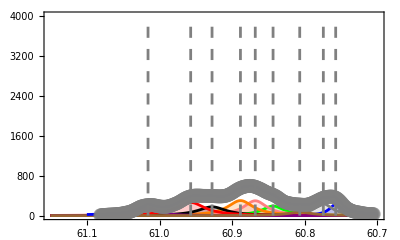

```mathematica
fit5=NonlinearModelFit[MB48h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale4,x,ppmavg4,width4]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]+Lorentzian[scale2a,x,ppmavg2a,width2a]},{{scale1,6.6},{scale2,13.4},{scale3,23.2},{scale4,16},{scale5,16},{scale6,12.3},{scale7,19},{scale8,7.3},{scale2a,1},{ppmavg1,60.7587},{ppmavg2,60.76},{ppmavg3,60.8474},{ppmavg4,60.87},{ppmavg5,60.8985},{ppmavg6,60.93},{ppmavg7,60.9612},{ppmavg8,61.0303},{ppmavg2a,60.81},{width1,0.02},{width2,0.03},{width3,0.06},{width4,0.04},{width5,0.04},{width6,0.04},{width7,0.05},{width8,0.03},{width2a,0.01}},x]
fit5["BestFitParameters"]
fit5["RSquared"]
fit5["ParameterTable"]
fit5["ANOVATable"]
individualMB48h=Plot[{Lorentzian[fit5["BestFitParameters"][[1]][[2]],ppm,fit5["BestFitParameters"][[10]][[2]],fit5["BestFitParameters"][[19]][[2]]],Lorentzian[fit5["BestFitParameters"][[2]][[2]],ppm,fit5["BestFitParameters"][[11]][[2]],fit5["BestFitParameters"][[20]][[2]]],Lorentzian[fit5["BestFitParameters"][[3]][[2]],ppm,fit5["BestFitParameters"][[12]][[2]],fit5["BestFitParameters"][[21]][[2]]],Lorentzian[fit5["BestFitParameters"][[4]][[2]],ppm,fit5["BestFitParameters"][[13]][[2]],fit5["BestFitParameters"][[22]][[2]]],Lorentzian[fit5["BestFitParameters"][[5]][[2]],ppm,fit5["BestFitParameters"][[14]][[2]],fit5["BestFitParameters"][[23]][[2]]],Lorentzian[fit5["BestFitParameters"][[6]][[2]],ppm,fit5["BestFitParameters"][[15]][[2]],fit5["BestFitParameters"][[24]][[2]]],Lorentzian[fit5["BestFitParameters"][[7]][[2]],ppm,fit5["BestFitParameters"][[16]][[2]],fit5["BestFitParameters"][[25]][[2]]],Lorentzian[fit5["BestFitParameters"][[8]][[2]],ppm,fit5["BestFitParameters"][[17]][[2]],fit5["BestFitParameters"][[26]][[2]]],Lorentzian[fit5["BestFitParameters"][[9]][[2]],ppm,fit5["BestFitParameters"][[18]][[2]],fit5["BestFitParameters"][[27]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,975.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Pink,Orange,Black,Red,Purple,Brown},AspectRatio->0.6];
cumulativeMB48h=Plot[Lorentzian[fit5["BestFitParameters"][[1]][[2]],ppm,fit5["BestFitParameters"][[10]][[2]],fit5["BestFitParameters"][[19]][[2]]]+Lorentzian[fit5["BestFitParameters"][[2]][[2]],ppm,fit5["BestFitParameters"][[11]][[2]],fit5["BestFitParameters"][[20]][[2]]]+Lorentzian[fit5["BestFitParameters"][[3]][[2]],ppm,fit5["BestFitParameters"][[12]][[2]],fit5["BestFitParameters"][[21]][[2]]]+Lorentzian[fit5["BestFitParameters"][[4]][[2]],ppm,fit5["BestFitParameters"][[13]][[2]],fit5["BestFitParameters"][[22]][[2]]]+Lorentzian[fit5["BestFitParameters"][[5]][[2]],ppm,fit5["BestFitParameters"][[14]][[2]],fit5["BestFitParameters"][[23]][[2]]]+Lorentzian[fit5["BestFitParameters"][[6]][[2]],ppm,fit5["BestFitParameters"][[15]][[2]],fit5["BestFitParameters"][[24]][[2]]]+Lorentzian[fit5["BestFitParameters"][[7]][[2]],ppm,fit5["BestFitParameters"][[16]][[2]],fit5["BestFitParameters"][[25]][[2]]]+Lorentzian[fit5["BestFitParameters"][[8]][[2]],ppm,fit5["BestFitParameters"][[17]][[2]],fit5["BestFitParameters"][[26]][[2]]]+Lorentzian[fit5["BestFitParameters"][[9]][[2]],ppm,fit5["BestFitParameters"][[18]][[2]],fit5["BestFitParameters"][[27]][[2]]],{ppm,60.7,61.1},PlotRange->{{60.7,61.1},{0,650.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB48h,cumulativeMB48h,dashed,ListPlot[MB48h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{0,500.}},Axes->{True,False},PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

```mathematica
Areas[scale_,width_]:=scale Sqrt[1/(width^2)]
```

```mathematica
allMBp5=Sum[Areas[fit1["BestFitParameters"][[ii]][[2]],fit1["BestFitParameters"][[ii+14]][[2]]],{ii,1,7}];
MBp5peak1=Areas[fit1["BestFitParameters"][[1]][[2]],fit1["BestFitParameters"][[15]][[2]]]/allMBp5
MBp5peak2=Areas[fit1["BestFitParameters"][[2]][[2]],fit1["BestFitParameters"][[16]][[2]]]/allMBp5
MBp5peak3=Areas[fit1["BestFitParameters"][[3]][[2]],fit1["BestFitParameters"][[17]][[2]]]/allMBp5
MBp5peak5=Areas[fit1["BestFitParameters"][[4]][[2]],fit1["BestFitParameters"][[18]][[2]]]/allMBp5
MBp5peak6=Areas[fit1["BestFitParameters"][[5]][[2]],fit1["BestFitParameters"][[19]][[2]]]/allMBp5
MBp5peak7=Areas[fit1["BestFitParameters"][[6]][[2]],fit1["BestFitParameters"][[20]][[2]]]/allMBp5
MBp5peak8=Areas[fit1["BestFitParameters"][[7]][[2]],fit1["BestFitParameters"][[21]][[2]]]/allMBp5
```

0.227369

0.113531

0.127564

0.120636

0.121796

0.175183

0.11392

```mathematica
allMB1=Sum[Areas[fit2["BestFitParameters"][[ii]][[2]],fit2["BestFitParameters"][[ii+14]][[2]]],{ii,1,7}];
MB1peak1=Areas[fit2["BestFitParameters"][[1]][[2]],fit2["BestFitParameters"][[15]][[2]]]/allMB1
MB1peak2=Areas[fit2["BestFitParameters"][[2]][[2]],fit2["BestFitParameters"][[16]][[2]]]/allMB1
MB1peak3=Areas[fit2["BestFitParameters"][[3]][[2]],fit2["BestFitParameters"][[17]][[2]]]/allMB1
MB1peak5=Areas[fit2["BestFitParameters"][[4]][[2]],fit2["BestFitParameters"][[18]][[2]]]/allMB1
MB1peak6=Areas[fit2["BestFitParameters"][[5]][[2]],fit2["BestFitParameters"][[19]][[2]]]/allMB1
MB1peak7=Areas[fit2["BestFitParameters"][[6]][[2]],fit2["BestFitParameters"][[20]][[2]]]/allMB1
MB1peak8=Areas[fit2["BestFitParameters"][[7]][[2]],fit2["BestFitParameters"][[21]][[2]]]/allMB1
```

0.227155

0.118698

0.132824

0.12999

0.0975375

0.179313

0.114483

```mathematica
allMB6=Sum[Areas[fit3["BestFitParameters"][[ii]][[2]],fit3["BestFitParameters"][[ii+18]][[2]]],{ii,1,9}];
MB6peak1=Areas[fit3["BestFitParameters"][[1]][[2]],fit3["BestFitParameters"][[19]][[2]]]/allMB6
MB6peak2=Areas[fit3["BestFitParameters"][[2]][[2]],fit3["BestFitParameters"][[20]][[2]]]/allMB6
MB6peak3=Areas[fit3["BestFitParameters"][[3]][[2]],fit3["BestFitParameters"][[21]][[2]]]/allMB6
MB6peak4=Areas[fit3["BestFitParameters"][[4]][[2]],fit3["BestFitParameters"][[22]][[2]]]/allMB6
MB6peak5=Areas[fit3["BestFitParameters"][[5]][[2]],fit3["BestFitParameters"][[23]][[2]]]/allMB6
MB6peak6=Areas[fit3["BestFitParameters"][[6]][[2]],fit3["BestFitParameters"][[24]][[2]]]/allMB6
MB6peak7=Areas[fit3["BestFitParameters"][[7]][[2]],fit3["BestFitParameters"][[25]][[2]]]/allMB6
MB6peak8=Areas[fit3["BestFitParameters"][[8]][[2]],fit3["BestFitParameters"][[26]][[2]]]/allMB6
MB6peak2a=Areas[fit3["BestFitParameters"][[9]][[2]],fit3["BestFitParameters"][[27]][[2]]]/allMB6
```

0.206156

0.115152

0.130081

0.0581777

0.116492

0.0910928

0.168055

0.110503

0.0042903

```mathematica
allMB24=Sum[Areas[fit4["BestFitParameters"][[ii]][[2]],fit4["BestFitParameters"][[ii+18]][[2]]],{ii,1,9}];
MB24peak1=Areas[fit4["BestFitParameters"][[1]][[2]],fit4["BestFitParameters"][[19]][[2]]]/allMB24
MB24peak2=Areas[fit4["BestFitParameters"][[2]][[2]],fit4["BestFitParameters"][[20]][[2]]]/allMB24
MB24peak3=Areas[fit4["BestFitParameters"][[3]][[2]],fit4["BestFitParameters"][[21]][[2]]]/allMB24
MB24peak4=Areas[fit4["BestFitParameters"][[4]][[2]],fit4["BestFitParameters"][[22]][[2]]]/allMB24
MB24peak5=Areas[fit4["BestFitParameters"][[5]][[2]],fit4["BestFitParameters"][[23]][[2]]]/allMB24
MB24peak6=Areas[fit4["BestFitParameters"][[6]][[2]],fit4["BestFitParameters"][[24]][[2]]]/allMB24
MB24peak7=Areas[fit4["BestFitParameters"][[7]][[2]],fit4["BestFitParameters"][[25]][[2]]]/allMB24
MB24peak8=Areas[fit4["BestFitParameters"][[8]][[2]],fit4["BestFitParameters"][[26]][[2]]]/allMB24
MB24peak2a=Areas[fit4["BestFitParameters"][[9]][[2]],fit4["BestFitParameters"][[27]][[2]]]/allMB24
```

0.174095

0.12234

0.121392

0.107208

0.112916

0.0689274

0.163938

0.104042

0.0251419

```mathematica
allMB48=Sum[Areas[fit5["BestFitParameters"][[ii]][[2]],fit5["BestFitParameters"][[ii+18]][[2]]],{ii,1,9}];
MB48peak1=Areas[fit5["BestFitParameters"][[1]][[2]],fit5["BestFitParameters"][[19]][[2]]]/allMB48
MB48peak2=Areas[fit5["BestFitParameters"][[2]][[2]],fit5["BestFitParameters"][[20]][[2]]]/allMB48
MB48peak3=Areas[fit5["BestFitParameters"][[3]][[2]],fit5["BestFitParameters"][[21]][[2]]]/allMB48
MB48peak4=Areas[fit5["BestFitParameters"][[4]][[2]],fit5["BestFitParameters"][[22]][[2]]]/allMB48
MB48peak5=Areas[fit5["BestFitParameters"][[5]][[2]],fit5["BestFitParameters"][[23]][[2]]]/allMB48
MB48peak6=Areas[fit5["BestFitParameters"][[6]][[2]],fit5["BestFitParameters"][[24]][[2]]]/allMB48
MB48peak7=Areas[fit5["BestFitParameters"][[7]][[2]],fit5["BestFitParameters"][[25]][[2]]]/allMB48
MB48peak8=Areas[fit5["BestFitParameters"][[8]][[2]],fit5["BestFitParameters"][[26]][[2]]]/allMB48
MB48peak2a=Areas[fit5["BestFitParameters"][[9]][[2]],fit5["BestFitParameters"][[27]][[2]]]/allMB48
```

0.116092

0.123097

0.100295

0.155314

0.157343

0.0919105

0.137881

0.0814322

0.0366356

```mathematica
peak1={{30./60.,MBp5peak1},{1.,MB1peak1},{6.,MB6peak1},{24.,MB24peak1},{48.,MB48peak1}};
peak2={{30./60.,MBp5peak2},{1.,MB1peak2},{6.,MB6peak2},{24.,MB24peak2},{48.,MB48peak2}};
peak3={{30./60.,MBp5peak3},{1.,MB1peak3},{6.,MB6peak3},{24.,MB24peak3},{48.,MB48peak3}};
peak4={{0.5,0},{1,0},{6.,MB6peak4},{24.,MB24peak4},{48.,MB48peak4}};
peak5={{30./60.,MBp5peak5},{1.,MB1peak5},{6.,MB6peak5},{24.,MB24peak5},{48.,MB48peak5}};
peak6={{30./60.,MBp5peak6},{1.,MB1peak6},{6.,MB6peak6},{24.,MB24peak6},{48.,MB48peak6}};
peak7={{30./60.,MBp5peak7},{1.,MB1peak7},{6.,MB6peak7},{24.,MB24peak7},{48.,MB48peak7}};
peak8={{30./60.,MBp5peak8},{1.,MB1peak8},{6.,MB6peak8},{24.,MB24peak8},{48.,MB48peak8}};
peak2a={{0.5,0},{1,0},{6.,MB6peak2a},{24,MB24peak2a},{48,MB48peak2a}};
```

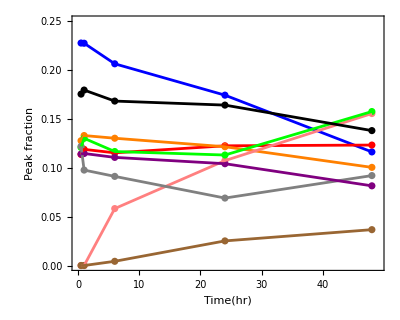

```mathematica
SetOptions[ListPlot, Frame->{{True,False},{True,False}},FrameTicks->{{LinTicks,None},{LinTicks,None}}, FrameStyle->Black, AspectRatio->0.8, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];
SetOptions[Plot, Frame->{{True,False},{True,False}}, FrameTicks->{{LinTicks,None},{LinTicks,None}},FrameStyle->Black, AspectRatio->0.8, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];

points=ListPlot[{peak1,peak2,peak3,peak4,peak5,peak6,peak7,peak8,peak2a}, FrameLabel->{{"Peak fraction",None},{
"Time(hr)",None}}, PlotRange->{{0,49},{0.,0.25}},PlotStyle->{Blue,Red,Orange,Pink,Green,Gray,Black,Purple,Brown},AspectRatio->0.8]; lines=ListPlot[{peak1,peak2,peak3,peak4,peak5,peak6,peak7,peak8,peak2a},Joined->True,PlotStyle->{Blue,Red,Orange,Pink,Green,Gray,Black,Purple,Brown}, PlotRange->{{0,50},{0.,0.3}}]; Show[{points,lines}]
```

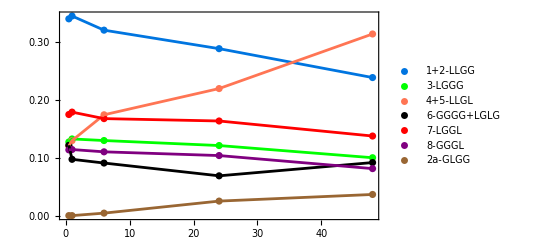

-Graphics-

```mathematica
peak1p2={{30./60.,MBp5peak1+MBp5peak2},{1.,MB1peak1+MB1peak2},{6.,MB6peak1+MB6peak2},{24.,MB24peak1+MB6peak2},{48.,MB48peak1+MB48peak2}};
peak4p5={{30./60.,MBp5peak5},{1.,MB1peak5},{6.,MB6peak5+MB6peak4},{24.,MB24peak5+MB24peak4},{48.,MB48peak5+MB48peak5}};

points2=ListPlot[{peak1p2,peak3,peak4p5,peak6,peak7,peak8,peak2a},PlotLegends->{"1+2-LLGG","3-LGGG","4+5-LLGL","6-GGGG+LGLG","7-LGGL","8-GGGL","2a-GLGG"},PlotStyle->{RGBColor[0,0.46,0.88],Green,RGBColor[1,0.46,0.33],Black,Red,Purple,Brown},AspectRatio->0.6]; lines2=ListPlot[{peak1p2,peak3,peak4p5,peak6,peak7,peak8,peak2a},Joined->True,PlotStyle->{RGBColor[0,0.46,0.88],Green,RGBColor[1,0.46,0.33],Black,Red,Purple,Brown}, PlotRange->{{0,50},{0.,0.4}}]; 
Show[{points2,lines2}]
Export["output.csv",peak1p2];
```

```mathematica
(*The excel file referenced here and stochastic model data used to populate the excel spreadsheet are publicly available at https://doi.org/10.18738/T8/QYLE8E. The stochastic model data file used to calculate the values plotted here is called 7525_008kT.seq*)
Stopeak1 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,3}}];
Stopeak2 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,4}}];
Stopeak3 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,5}}];
Stopeak4 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,6}}];
Stopeak5 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,7}}];
Stopeak6 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,8}}];
Stopeak7 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,9}}];
Stopeak8 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,10}}];
Stopeak1p7 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",1,21;;37,{1,23}}];

SetOptions[ListPlot, Frame->{{True,False},{True,False}},FrameTicks->{{LinTicks,None},{LinTicks,None}}, FrameStyle->Black, AspectRatio->0.8, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];
SetOptions[Plot, Frame->{{True,False},{True,False}}, FrameTicks->{{LinTicks,None},{LinTicks,None}},FrameStyle->Black, AspectRatio->1, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];
```

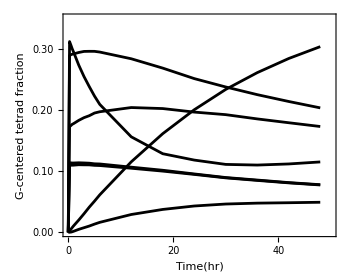

```mathematica
stolines = ListPlot[{Stopeak1p7,Stopeak2,Stopeak3,Stopeak4,Stopeak5,Stopeak6,Stopeak8},Joined->True,PlotStyle->Black,FrameLabel->{{"G-centered tetrad fraction",None},{"Time(hr)",None}},PlotRange->{{0,50},{0.,0.3501}},AspectRatio->0.8]
(*PlotStyle->{Black,Purple,Brown,RGBColor[0,0.46,0.88],Directive[Green,Dashed],Red,RGBColor[1,0.46,0.33]}*)
```